Cost of NVIDIA V100 Google Cloud per hour

```mathematica
2.28
```

2.28

training on 512 NVIDIA V100 GPU for 10 days

```mathematica
2.28 24 10 512
```

280166.

```mathematica
3.14 10^23/(7 10^12)/3600
```

1.24603×10^7

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\ugo\Desktop\Daten contact\Research\KI\NLP Models

```mathematica
data=Import["NLP_Models.xlsx"][[1]];
```

```mathematica
tdata=data[[2;;-1,{1,2,4}]] ;(*First, second and fourth column, first row discarded*)
```

```mathematica
modelnames=tdata[[All,1]]
```

{Ulmfit,ELMO,BERT,GPT-2,XLNet-Large,RoBERTa,Megatron-LM,ALBERT,T5,BART,PEGASUS,GPT-3,Turing-NLG,ELECTRA,Megatron-Turing NLG,Gopher,M6-10T}

```mathematica
sizes=tdata[[All,3]];
```

```mathematica
sizetoword[n_]:=If[n<10^9,IntegerString[Round[n/10^6]]<>"M",IntegerString[Round[n/10^9]]<>"B"]
```

```mathematica
sizetoword/@sizes
```

{3M,94M,340M,2B,340M,340M,8B,235M,11B,380M,568M,175B,17B,340M,530B,280B,10000B}

```mathematica
annotations={modelnames,sizetoword/@sizes}//Transpose//Map[StringJoin[#[[1]]," ",#[[2]]]&]
```

{Ulmfit 3M,ELMO 94M,BERT 340M,GPT-2 2B,XLNet-Large 340M,RoBERTa 340M,Megatron-LM 8B,ALBERT 235M,T5 11B,BART 380M,PEGASUS 568M,GPT-3 175B,Turing-NLG 17B,ELECTRA 340M,Megatron-Turing NLG 530B,Gopher 280B,M6-10T 10000B}

```mathematica
tabledata=tdata[[All,{2,3}]]
```

{{Thu 18 Jan 2018 00:00:00GMT+2,3.×10^6},{Thu 15 Feb 2018 00:00:00GMT+2,9.4×10^7},{Thu 11 Oct 2018 00:00:00GMT+2,3.4×10^8},{Thu 14 Feb 2019 00:00:00GMT+2,1.5×10^9},{Wed 19 Jun 2019 00:00:00GMT+2,3.4×10^8},{Fri 26 Jul 2019 00:00:00GMT+2,3.4×10^8},{Tue 17 Sep 2019 00:00:00GMT+2,8.3×10^9},{Thu 26 Sep 2019 00:00:00GMT+2,2.35×10^8},{Wed 23 Oct 2019 00:00:00GMT+2,1.1×10^10},{Tue 29 Oct 2019 00:00:00GMT+2,3.8×10^8},{Wed 18 Dec 2019 00:00:00GMT+2,5.68×10^8},{Thu 28 May 2020 00:00:00GMT+2,1.75×10^11},{Thu 13 Feb 2020 00:00:00GMT+2,1.7×10^10},{Mon 23 Mar 2020 00:00:00GMT+2,3.4×10^8},{Mon 28 Feb 2022 00:00:00GMT+2,5.3×10^11},{Wed 8 Dec 2021 00:00:00GMT+2,2.8×10^11},{Fri 8 Oct 2021 00:00:00GMT+2,1.×10^13}}

```mathematica
logdata=Map[{#[[1]],#[[2]]/10^9}&,tabledata]
```

{{Thu 18 Jan 2018 00:00:00GMT+2,0.003},{Thu 15 Feb 2018 00:00:00GMT+2,0.094},{Thu 11 Oct 2018 00:00:00GMT+2,0.34},{Thu 14 Feb 2019 00:00:00GMT+2,1.5},{Wed 19 Jun 2019 00:00:00GMT+2,0.34},{Fri 26 Jul 2019 00:00:00GMT+2,0.34},{Tue 17 Sep 2019 00:00:00GMT+2,8.3},{Thu 26 Sep 2019 00:00:00GMT+2,0.235},{Wed 23 Oct 2019 00:00:00GMT+2,11.},{Tue 29 Oct 2019 00:00:00GMT+2,0.38},{Wed 18 Dec 2019 00:00:00GMT+2,0.568},{Thu 28 May 2020 00:00:00GMT+2,175.},{Thu 13 Feb 2020 00:00:00GMT+2,17.},{Mon 23 Mar 2020 00:00:00GMT+2,0.34},{Mon 28 Feb 2022 00:00:00GMT+2,530.},{Wed 8 Dec 2021 00:00:00GMT+2,280.},{Fri 8 Oct 2021 00:00:00GMT+2,10000.}}

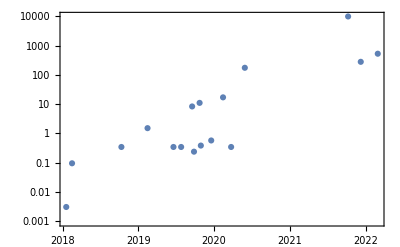

```mathematica
DateListLogPlot[logdata, PlotRange->All,PlotMarkers->Automatic,Joined->False]
```

```mathematica
labeledlogdata=Table[
	Labeled[
		logdata[[i]],Text[Style[annotations[[i]],10]]],{i,1,Length[logdata]}]
```

{{Thu 18 Jan 2018 00:00:00GMT+2,0.003}Ulmfit 3M,{Thu 15 Feb 2018 00:00:00GMT+2,0.094}ELMO 94M,{Thu 11 Oct 2018 00:00:00GMT+2,0.34}BERT 340M,{Thu 14 Feb 2019 00:00:00GMT+2,1.5}GPT-2 2B,{Wed 19 Jun 2019 00:00:00GMT+2,0.34}XLNet-Large 340M,{Fri 26 Jul 2019 00:00:00GMT+2,0.34}RoBERTa 340M,{Tue 17 Sep 2019 00:00:00GMT+2,8.3}Megatron-LM 8B,{Thu 26 Sep 2019 00:00:00GMT+2,0.235}ALBERT 235M,{Wed 23 Oct 2019 00:00:00GMT+2,11.}T5 11B,{Tue 29 Oct 2019 00:00:00GMT+2,0.38}BART 380M,{Wed 18 Dec 2019 00:00:00GMT+2,0.568}PEGASUS 568M,{Thu 28 May 2020 00:00:00GMT+2,175.}GPT-3 175B,{Thu 13 Feb 2020 00:00:00GMT+2,17.}Turing-NLG 17B,{Mon 23 Mar 2020 00:00:00GMT+2,0.34}ELECTRA 340M,{Mon 28 Feb 2022 00:00:00GMT+2,530.}Megatron-Turing NLG 530B,{Wed 8 Dec 2021 00:00:00GMT+2,280.}Gopher 280B,{Fri 8 Oct 2021 00:00:00GMT+2,10000.}M6-10T 10000B}

```mathematica
calloutlogdata=Table[
	Callout[
		logdata[[i]],Text[Style[annotations[[i]],14]],LabelVisibility->All],{i,1,Length[logdata]}]
```

{Callout[{Thu 18 Jan 2018 00:00:00GMT+2,0.003},Ulmfit 3M,LabelVisibility→All],Callout[{Thu 15 Feb 2018 00:00:00GMT+2,0.094},ELMO 94M,LabelVisibility→All],Callout[{Thu 11 Oct 2018 00:00:00GMT+2,0.34},BERT 340M,LabelVisibility→All],Callout[{Thu 14 Feb 2019 00:00:00GMT+2,1.5},GPT-2 2B,LabelVisibility→All],Callout[{Wed 19 Jun 2019 00:00:00GMT+2,0.34},XLNet-Large 340M,LabelVisibility→All],Callout[{Fri 26 Jul 2019 00:00:00GMT+2,0.34},RoBERTa 340M,LabelVisibility→All],Callout[{Tue 17 Sep 2019 00:00:00GMT+2,8.3},Megatron-LM 8B,LabelVisibility→All],Callout[{Thu 26 Sep 2019 00:00:00GMT+2,0.235},ALBERT 235M,LabelVisibility→All],Callout[{Wed 23 Oct 2019 00:00:00GMT+2,11.},T5 11B,LabelVisibility→All],Callout[{Tue 29 Oct 2019 00:00:00GMT+2,0.38},BART 380M,LabelVisibility→All],Callout[{Wed 18 Dec 2019 00:00:00GMT+2,0.568},PEGASUS 568M,LabelVisibility→All],Callout[{Thu 28 May 2020 00:00:00GMT+2,175.},GPT-3 175B,LabelVisibility→All],Callout[{Thu 13 Feb 2020 00:00:00GMT+2,17.},Turing-NLG 17B,LabelVisibility→All],Callout[{Mon 23 Mar 2020 00:00:00GMT+2,0.34},ELECTRA 340M,LabelVisibility→All],Callout[{Mon 28 Feb 2022 00:00:00GMT+2,530.},Megatron-Turing NLG 530B,LabelVisibility→All],Callout[{Wed 8 Dec 2021 00:00:00GMT+2,280.},Gopher 280B,LabelVisibility→All],Callout[{Fri 8 Oct 2021 00:00:00GMT+2,10000.},M6-10T 10000B,LabelVisibility→All]}

```mathematica
finetunedlogdata={Callout[{DateObject[{2018,1,18,0,0,0.},"Instant","Gregorian",2.],0.003},"Ulmfit 3M",LabelVisibility->All],Callout[{DateObject[{2018,2,15,0,0,0.},"Instant","Gregorian",2.],0.094},"ELMO 94M",LabelVisibility->All],Callout[{DateObject[{2018,10,11,0,0,0.},"Instant","Gregorian",2.],0.34},"BERT 340M",LabelVisibility->All],Callout[{DateObject[{2019,2,14,0,0,0.},"Instant","Gregorian",2.],1.5},"GPT-2 2B",LabelVisibility->All],Callout[{DateObject[{2019,6,19,0,0,0.},"Instant","Gregorian",2.],0.34},"XLNet-Large 340M",Before,LabelVisibility->All],Callout[{DateObject[{2019,7,26,0,0,0.},"Instant","Gregorian",2.],0.34},"RoBERTa 340M",Below,LabelVisibility->All],Callout[{DateObject[{2019,9,17,0,0,0.},"Instant","Gregorian",2.],8.3},"Megatron-LM 8B",LabelVisibility->All],Callout[{DateObject[{2019,9,26,0,0,0.},"Instant","Gregorian",2.],0.23500000000000001},"ALBERT 235M",After,LabelVisibility->All],Callout[{DateObject[{2019,10,23,0,0,0.},"Instant","Gregorian",2.],11.},"T5 11B",LabelVisibility->All],
Callout[{DateObject[{2019,10,29,0,0,0.},"Instant","Gregorian",2.],0.38},"BART 380M",LabelVisibility->All],Callout[{DateObject[{2019,12,18,0,0,0.},"Instant","Gregorian",2.],0.5680000000000001},"PEGASUS 568M",LabelVisibility->All],Callout[{DateObject[{2020,5,28,0,0,0.},"Instant","Gregorian",2.],175.},"GPT-3 175B",LabelVisibility->All],Callout[{DateObject[{2020,2,13,0,0,0.},"Instant","Gregorian",2.],17.},"Turing-NLG 17B",LabelVisibility->All],Callout[{DateObject[{2020,3,23,0,0,0.},"Instant","Gregorian",2.],0.34},"ELECTRA 340M",LabelVisibility->All],Callout[{DateObject[{2022,2,28,0,0,0.},"Instant","Gregorian",2.],530.},"Megatron-Turing NLG 530B",LabelVisibility->All],Callout[{DateObject[{2021,12,8,0,0,0.},"Instant","Gregorian",2.],280.},"Gopher 280B",LabelVisibility->All],Callout[{DateObject[{2021,10,8,0,0,0.},"Instant","Gregorian",2.],10000.},"M6-10T 10000B",LabelVisibility->All]};
```

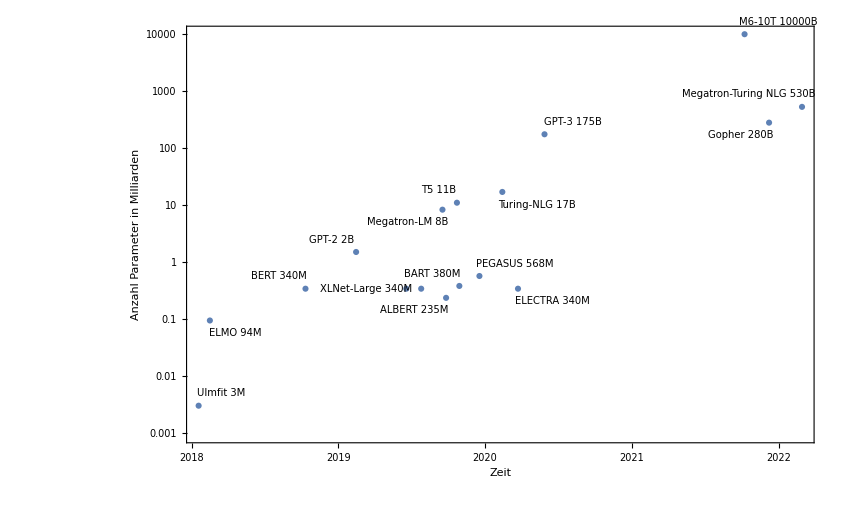

```mathematica
p1=DateListLogPlot[labeledlogdata, 
	PlotRange->All,
	PlotMarkers->Automatic,
	Joined->False,
	FrameLabel->{{Text[Style["Anzahl Parameter in Milliarden",Bold,12]],None},{Text[Style["Zeit",Bold,12]],None}},
	LabelStyle-> Directive[Black, 10],ImageSize->Full]
```

```mathematica
p2=DateListLogPlot[finetunedlogdata, 
	PlotRange->All,
	PlotMarkers->Automatic,
	Joined->False,
	FrameLabel->{{Text[Style["Number of Parameters [10^9]",18]],None},{Text[Style["Time",18]],None}},
	LabelStyle-> Directive[Black, 14],
	DateTicksFormat->{"Year"},
	FrameTicks->{{{0.01,0.1,1,10,100,1000,10000},None},{Automatic,None}},
	ImageSize->Full]
```

-Graphics-

```mathematica
absdata={AbsoluteTime[#[[1]]],Log10[#[[2]]]}&/@logdata
```

{{3725222400,-2.52288},{3727641600,-1.02687},{3748204800,-0.468521},{3759091200,0.176091},{3769891200,-0.468521},{3773088000,-0.468521},{3777667200,0.919078},{3778444800,-0.628932},{3780777600,1.04139},{3781296000,-0.420216},{3785616000,-0.245652},{3799612800,2.24304},{3790540800,1.23045},{3793910400,-0.468521},{3854995200,2.72428},{3847910400,2.44716},{3842640000,4.}}

```mathematica
timedata=absdata[[All,1]]
```

{3725222400,3727641600,3748204800,3759091200,3769891200,3773088000,3777667200,3778444800,3780777600,3781296000,3785616000,3799612800,3790540800,3793910400,3854995200,3847910400,3842640000}

```mathematica
mint=Min[absdata[[All,1]]];maxt=Max[absdata[[All,1]]];
```

```mathematica
lm=LinearModelFit[absdata,x,x]//Normal
```

-145.479+3.85661×10^-8 x

```mathematica
lmf=Function[y,lm/. x->y]
```

Function[y,lm/.x→y]

```mathematica
regline={DateObject/@timedata,Power[10,lmf/@ timedata]}//Transpose
```

{{Thu 18 Jan 2018 00:00:00GMT+2,0.0154193},{Thu 15 Feb 2018 00:00:00GMT+2,0.0191145},{Thu 11 Oct 2018 00:00:00GMT+2,0.118688},{Thu 14 Feb 2019 00:00:00GMT+2,0.31207},{Wed 19 Jun 2019 00:00:00GMT+2,0.814266},{Fri 26 Jul 2019 00:00:00GMT+2,1.08157},{Tue 17 Sep 2019 00:00:00GMT+2,1.62426},{Thu 26 Sep 2019 00:00:00GMT+2,1.74038},{Wed 23 Oct 2019 00:00:00GMT+2,2.14098},{Tue 29 Oct 2019 00:00:00GMT+2,2.24184},{Wed 18 Dec 2019 00:00:00GMT+2,3.29011},{Thu 28 May 2020 00:00:00GMT+2,11.4028},{Thu 13 Feb 2020 00:00:00GMT+2,5.09496},{Mon 23 Mar 2020 00:00:00GMT+2,6.87216},{Mon 28 Feb 2022 00:00:00GMT+2,1559.18},{Wed 8 Dec 2021 00:00:00GMT+2,831.119},{Fri 8 Oct 2021 00:00:00GMT+2,520.48}}

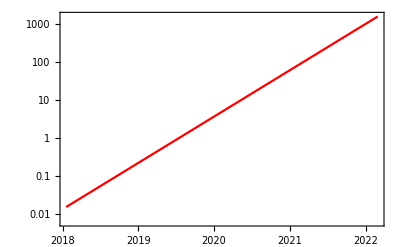

```mathematica
regplot=DateListLogPlot[regline,PlotStyle->Red]
```

```mathematica
completePlot=Show[p2,regplot]
```

-Graphics-

```mathematica
Export["nlp_models_sizes_over_time.png",completePlot,ImageSize->{1200,720}];
```

```mathematica
Export["nlp_models_sizes_over_time.svg",completePlot,ImageSize->{1200,720}];
```

```mathematica
582/936.
```

0.621795

```mathematica
1200 0.6
```

720.